```mathematica
Integrate[ ff[t_] E^(-s t),{t,0,Infinity}]
```

∫_0^∞ ⅇ^(-s t) ff[t_]ⅆt

```mathematica
Integrate[ E^(-s x) x^(k-1),x]/.x->10
```

-s^-k Gamma[k,10 s]

```mathematica
Integrate[ (x)^(-s-1) Log[x]^(k-1),x]/.x->10
```

-s^-k Gamma[k,s Log[10]]

```mathematica
Integrate[  E^(-s t),{t,0,Infinity}]
```

ConditionalExpression[1/s,Re[s]>0]

```mathematica
Integrate[ t^(-s-1) Log[t]^(k-1),{t,1,Infinity}]
```

ConditionalExpression[s^-k Gamma[k],Re[s]>0&&Re[k]>0]

```mathematica
Integrate[ E^(-s t) t^(k-1),{t,0,Infinity}]
```

ConditionalExpression[s^-k Gamma[k],Re[s]>0&&Re[k]>0]

```mathematica
Integrate[ t^(-s-1),{t,1,Infinity}]
```

ConditionalExpression[1/s,Re[s]>0]

```mathematica
Integrate[ t^(-s-1) Log[t],{t,1,Infinity}]
```

ConditionalExpression[1/s^2,Re[s]>0]

```mathematica
Integrate[LaguerreL[ t,x],x]
```

LaguerreL[t,x]-LaguerreL[1+t,x]

```mathematica
Integrate[ x^(s t),{t,0,Infinity}]
```

ConditionalExpression[-1/(s Log[x]),Re[s Log[x]]<0]

```mathematica
Integrate[ x^(s t),{t,0,Infinity}]
```

ConditionalExpression[-1/(s Log[x]),Re[s Log[x]]<0]

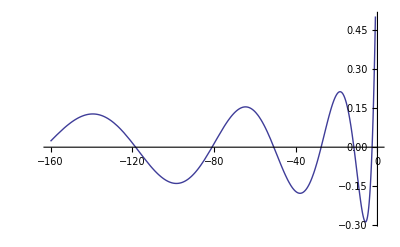

```mathematica
Plot[ LaguerreL[ t,Log[.5]],{t,-160,0}]
```

```mathematica
N@Integrate[ LaguerreL[ -t, Log[.5]],{t,0,600}]
```

2.40209

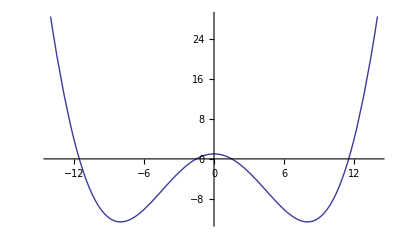

```mathematica
Plot[Re[ LaguerreL[t I,Log[3]]],{t,-14,14}]
```

```mathematica
gg[n_, rr_] := If[ rr==0,1, (-1)^(rr) Gamma[ rr,0,-Log[n]]/Gamma[rr]]
hh[n_, z_,t_:30] := Sum[ Binomial[z,k] gg[n,k],{k,0,t}]
```

```mathematica
Chop@N@hh[100,-4]
```

-0.167536

```mathematica
LaguerreL[4,Log[100.]]
```

-0.167536

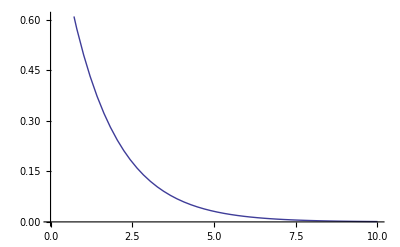

```mathematica
Plot[ .5^t,{t,0,10}]
```

```mathematica
D[ Log[x],x]/.x->(15)
```

1/15

```mathematica
N[Limit[ D[ LogIntegral[x]-Log[Log[x]]-EulerGamma,x], x->3I]]
```

0.441496-0.327838 ⅈ

```mathematica
Limit[ D[ LogIntegral[x],x], x->(15)]
```

1/Log[15]

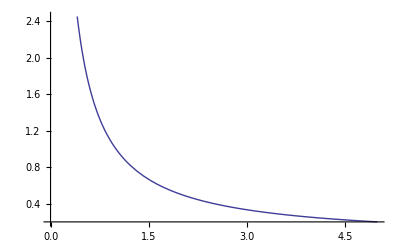

```mathematica
Plot[ D[ Log[x],x]/.x->y,{y,0,5}]
```

```mathematica
aa[x_] := LogIntegral[x]-Log[Log[x]]-EulerGamma
```

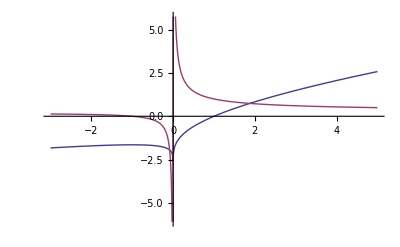

```mathematica
Plot[{Re[aa[y]], Re[D[aa[x],x]/.x->y]},{y,-3,5}]
```

```mathematica
D[ aa[x],x]/.x->5
```

4/(5 Log[5])

```mathematica
D[ aa[2x],x]
```

2/Log[2 x]-1/(x Log[2 x])

```mathematica
1/Log[x]-1/(x Log[x])
```

```mathematica
2/Log[2 x]-1/(x Log[2 x])
```

2/Log[2 x]-1/(x Log[2 x])

```mathematica
FullSimplify[2/Log[2 x]-1/(x Log[2 x])]
```

(-1+2 x)/(x Log[2 x])

```mathematica
Expand[(-1+2 x)/(x (Log[2]+Log[x]))]
```

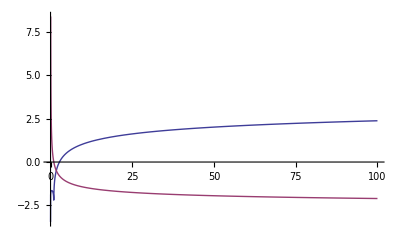

```mathematica
aaa[x_] := LogIntegral[x]-Log[Log[x]]-EulerGamma
Plot[{Re[aaa[Log@y]],Re[aaa[1/y]]},{y,0,100}]
```

```mathematica
(D[ ExpIntegralEi[Log@n]-Log@Log@n-EulerGamma,n]/.n->12)
```

11/(12 Log[12])

```mathematica
(D[ ExpIntegralEi[Log@n]-Log@Log@n-EulerGamma,n]/.n->1/12)
```

11/Log[12]

```mathematica
Log[x^(a+b)]
```

Log[x^(a+b)]

```mathematica
Log[ x^a]Log[x^b]
```

Log[x^a] Log[x^b]

```mathematica
Integrate[ z/(n Log[n])( LaguerreL[ -z-1, Log[n]]-LaguerreL[-z,Log[n]] ),{n,1,x}]
```

z (-z HypergeometricPFQ[{1,1,1+z},{2,2,2},Log[x]]+(1+z) HypergeometricPFQ[{1,1,2+z},{2,2,2},Log[x]]) Log[x]

```mathematica
N[Expand[z (-z HypergeometricPFQ[{1,1,1+z},{2,2,2},Log[x]]+(1+z) HypergeometricPFQ[{1,1,2+z},{2,2,2},Log[x]]) Log[x]/.{z->3,x->10}]]
```

81.5612

```mathematica
-1+N@LaguerreL[ -3,Log[10]]
```

81.5612

```mathematica
Integrate[ z/(n Log[n])( LaguerreL[ -z-1, Log[n]]-LaguerreL[-z,Log[n]] ),{n,0,x}]
```

1+z (-z HypergeometricPFQ[{1,1,1+z},{2,2,2},Log[x]]+(1+z) HypergeometricPFQ[{1,1,2+z},{2,2,2},Log[x]]) Log[x]

```mathematica
N[1+z (-z HypergeometricPFQ[{1,1,1+z},{2,2,2},Log[x]]+(1+z) HypergeometricPFQ[{1,1,2+z},{2,2,2},Log[x]]) Log[x]/.{z->3,x->10}]
```

82.5612+0. ⅈ

```mathematica
N@LaguerreL[ -3,Log[10]]
```

82.5612

```mathematica
Integrate[ z/(n Log[n])( LaguerreL[ -z-1, Log[n]]-LaguerreL[-z,Log[n]] ),{n,0,1}]
```

1

```mathematica
D[LaguerreL[-3,n],n]/.n->1
```

(13 ⅇ)/2

```mathematica
Integrate[ D[ LaguerreL[ -a, Log[x]],x] (LaguerreL[-b, Log[n]-Log[x]]),{x,1,n}]
```

∫_1^n -(LaguerreL[-b,Log[n]-Log[x]] LaguerreL[-1-a,1,Log[x]])/xⅆx

```mathematica
Integrate[ (a / (x Log[x])(LaguerreL[ -a-1,Log[x]]-LaguerreL[-a,Log[x]])) (LaguerreL[-b, Log[n]-Log[x]]),{x,1,n}]
```

∫_1^n (a (LaguerreL[-1-a,Log[x]]-LaguerreL[-a,Log[x]]) LaguerreL[-b,Log[n]-Log[x]])/(x Log[x])ⅆx

```mathematica
Integrate[ LaguerreL[ -b, Log[n/x]],{x,1,n}]
```

∫_1^n LaguerreL[-b,Log[n/x]]ⅆx

```mathematica
Integrate[ x,{x,50,100}]
```

3750

```mathematica
Integrate[ 50 50 x,{x,1,2}]
```

3750

```mathematica
N[Integrate[ z / (n Log[n]) (LaguerreL[-z-1, Log[n]]-LaguerreL[-z,Log[n]]),{n,x,x y}]/.{x->5,y->6,z->3}]
```

380.024

```mathematica
N[Integrate[ z / (x n Log[x n]) (LaguerreL[-z-1, Log[x n]]-LaguerreL[-z,Log[x n]]),{n,0,y}]/.{x->5,y->6,z->3}]
```

81.5188

```mathematica
N[Integrate[ z / (n Log[x n]) (LaguerreL[-z-1, Log[x n]]-LaguerreL[-z,Log[x n]]),{n,0,y}]/.{x->5,y->6,z->3}]
```

407.594

```mathematica
N[Integrate[ D[LaguerreL[-z,Log[n]],n],{n,x,x y}]/.{x->5,y->6,z->3}]
```

$Aborted

```mathematica
N[Integrate[ 1/Log[y]-1/(y Log[y]),{y,1,40}]]
```

13.957

```mathematica
N[Integrate[ 1/Log[y]-1/(y Log[y]),{y,1,5}]+Integrate[ 1/Log[y]-1/(y Log[y]),{y,5,40}]]
```

13.957

```mathematica
ff[n_] := N[Integrate[ 1/Log[y]-1/(y Log[y]),{y,1,n}]]
```

```mathematica
ff[40]
```

13.957

```mathematica
ff[5]+N[Integrate[ 1/Log[y]-1/(y Log[y]),{y,5,40}]]
```

13.957

```mathematica
ff[5]+N[Integrate[5(1/Log[5y]-1/((5y) Log[5y])),{y,1,8}]]
```

13.957

```mathematica
FullSimplify[Expand[x(1/Log[x y]-1/((x y) Log[x y]))]]
```

(-1+x y)/(y Log[x y])

```mathematica
Integrate[ (-1+x y)/(y Log[x y]),y]
```

-Log[Log[x y]]+LogIntegral[x y]

```mathematica
ff[5]+N[Integrate[5(5 y)/(5 y Log[5y])-5/((5y) Log[5y]),{y,1,8}]]
```

13.957

```mathematica
ff[5]+N[Integrate[(5(5 y)-5)/(5 y Log[5y]),{y,1,8}]]
```

13.957

```mathematica
ff[5]+N[Integrate[(5 y-1)/( y Log[5y]),{y,1,8}]]
```

13.957

```mathematica
Integrate[D[ x^z,x],{x,0,1}]
```

ConditionalExpression[1,Re[z]>0]

```mathematica
Integrate[D[ LaguerreL[ -z,Log[y]],y]/.y->x,{x,0,1}]
```

ConditionalExpression[1,Re[z]>0]

```mathematica
Integrate[ (1-E^-t)/t,{t,0,z}]
```

ConditionalExpression[EulerGamma+Gamma[0,z]+Log[z],Re[z]>0]

```mathematica
Integrate[ (E^-t)/t,{t,-z,Infinity}]
```

ConditionalExpression[Gamma[0,-z]+Log[-z],Im[z]≠0||z<0]

```mathematica
Sum[ Log[x]^k/k/k!,{k,1,Infinity}]
```

-EulerGamma-Gamma[0,-Log[x]]-Log[-Log[x]]

```mathematica
Sum[ (-1)^k Log[x]^k/k/k!,{k,1,Infinity}]
```

-EulerGamma-Gamma[0,Log[x]]-Log[Log[x]]

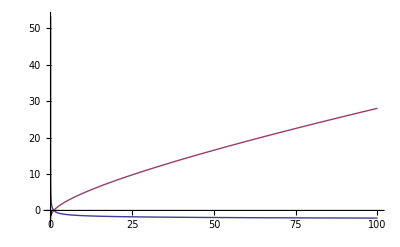

```mathematica
Plot[{-EulerGamma-Gamma[0,Log[x]]-Log[Log[x]],Re[-EulerGamma+LogIntegral[x]-Log[Log[x]]]}, {x,0,100}]
```

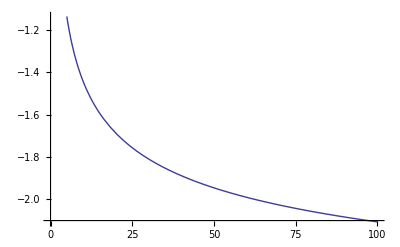

```mathematica
Plot[{Re[(-EulerGamma-Gamma[0,Log[x]]-Log[Log[x]])]}, {x,0,100}]
```

```mathematica
N[Sum[ (-1)^k Log[x]^k/k/k!,{k,1,Infinity}]/.x->1/10]
```

4.75435+0. ⅈ

```mathematica
N[Sum[ Log[x]^k/k/k!,{k,1,Infinity}]/.x->10]
```

4.75435+0. ⅈ

```mathematica
FullSimplify[D[x^z,x]/((x^(z+1)-x^z))]
```

z/((-1+x) x)

```mathematica
(x^(z+1)-x^z)
```

-x^z+x^(1+z)

```mathematica
(x^(-1+z) z)/(-x^z+x^(1+z))
```

(x^(-1+z) z)/(-x^z+x^(1+z))

```mathematica
D[ x^z,x]
```

x^(-1+z) z

```mathematica
FullSimplify[5/((-1+x) x)(x^6-x^5)]
```

5 x^4

```mathematica
ll[x_, z_] := LaguerreL[-z,Log[x]]
dl[x_, z_] := z/(x Log[x]) (ll[x,z+1]-ll[x,z])
gg[x_, z_] := (-1)^z Gamma[ z,0,-Log[x]]/Gamma[z]
```

```mathematica
D[gg[x,z],x]
```

-((-1)^z (-Log[x])^(-1+z))/Gamma[z]

```mathematica
D[ (x-1)^z,x]
```

(-1+x)^(-1+z) z

```mathematica
Binomial[z,k-1](k-1) + Binomial[z,k]k/.k->4
```

1/2 (-2+z) (-1+z) z+1/6 (-3+z) (-2+z) (-1+z) z

```mathematica
Binomial[z,3]
```

1/6 (-2+z) (-1+z) z

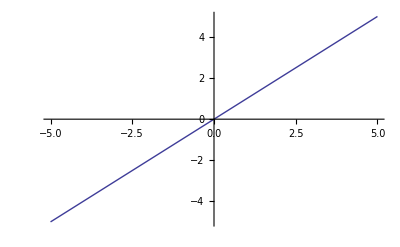

```mathematica
Plot[ D[ LaguerreL[-z,Log[x]],x]/.x->1,{z,-5,5}]
```

```mathematica
N[D[ LaguerreL[ -n,Log[x]],x]/.x->1]/.n->6
```

6.

```mathematica
FullSimplify[Limit[ dl[x,z],x->1]]
```

z

```mathematica
D[ x^z,x]
```

x^(-1+z) z

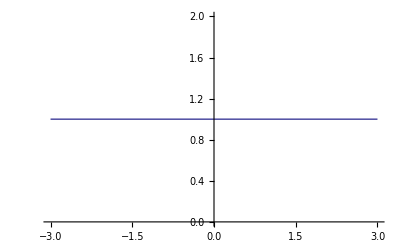

```mathematica
Plot[Re[ll[x,0]],{x,-3,3}]
```

```mathematica
N@dl[3,1]
```

1.

```mathematica
D[x^0,x]
```

0

```mathematica
D[gg[n,4],n]
```

Log[n]^3/6

```mathematica
D[(n-1)^5,n]
```

5 (-1+n)^4

```mathematica
D[LaguerreL[-z,Log[n]],{n,3}]
```

-LaguerreL[-3-z,3,Log[n]]/n^3-(3 LaguerreL[-2-z,2,Log[n]])/n^3-(2 LaguerreL[-1-z,1,Log[n]])/n^3

```mathematica
Integrate[ E^(t(1-s))z Hypergeometric1F1[1-z, 2,t],{t,-Log[x],0}]
```

∫_(-Log[x])^0 ⅇ^((1-s) t) z Hypergeometric1F1[1-z,2,t]ⅆt

```mathematica
1+N[z Integrate[ E^(t(s-1))Hypergeometric1F1[1-z, 2,t],{t,-Log[x],0}]/.{s->0, x->100, z->3}]
```

2081.41

```mathematica
1+N[z Integrate[ E^(-Log[t](s-1))Hypergeometric1F1[1-z, 2,-Log[t]],{t,1,x}]/.{s->0, x->100, z->3}]
```

119334.

```mathematica
LaguerreL[-3,0,Log[100.]]
```

2081.41

```mathematica
ff2[ n_, s_, z_, t_] := 1+Sum[ Binomial[z,k] 1/(s-1)^k ( Gamma[ k,0, (s-1)Log[n]]/Gamma[k]),{k,1, t}]
```

```mathematica
Chop@N@ff2[100,-1,3,30]
```

119334.

```mathematica
Hypergeometric1F1[3,1,Log[100.]]
```

2081.41

```mathematica
N@Hypergeometric1F1[-2, 2,Log[10]]
```

-0.418935

```mathematica
N[D[ LaguerreL[-3,Log[n]],n]/.n->100]
```

27.4193

```mathematica
D[ LaguerreL[-3,Log[n]],n]
```

-LaguerreL[-4,1,Log[n]]/n

```mathematica
N[3Hypergeometric1F1[ 4,2,Log[n]]/n/.n->100]
```

27.4193

```mathematica
N[-LaguerreL[-4,1,Log[n]]/n/.n->100]
```

27.4193

```mathematica
N[D[ LaguerreL[-z,Log[n]],n]/.{n->100,z->4}]
```

90.3236

```mathematica
N[z Hypergeometric1F1[ 1+z,2,Log[n]]/n/.{n->100,z->4}]
```

90.3236

```mathematica
N[1+3Integrate[n^-1 Hypergeometric1F1[ 1+3, 2, Log[n]],{n,1,100}]]
```

2081.41

```mathematica
LaguerreL[ -3, Log@100.]
```

2081.41

```mathematica
1+N[z Integrate[ E^(-Log[t](s-1))Hypergeometric1F1[1-z, 2,-Log[t]],{t,1,x}]/.{s->0, x->100, z->3}]
ff2[ n_, s_, z_, t_] := 1+Sum[ Binomial[z,k] 1/(s-1)^k ( Gamma[ k,0, (s-1)Log[n]]/Gamma[k]),{k,1, t}]
Chop@N@ff2[100,-1,3,30]
```

119334.

119334.

```mathematica
N[1+z Integrate[t^-s Hypergeometric1F1[1-z, 2,-Log[t]],{t,1,x}]/.{s->3, x->120, z->4}]
```

5.05842

```mathematica
ff2[ n_, s_, z_, t_] := 1+Sum[ Binomial[z,k] 1/(s-1)^k ( Gamma[ k,0, (s-1)Log[n]]/Gamma[k]),{k,1, t}]
Chop@N@ff2[120,3,4,30]
```

5.05842

```mathematica
1+z Integrate[ Hypergeometric1F1[1-z, 2,-Log[t]],{t,1,x}]/.{z->3, x->30}
```

1+3 (29/3+20 Log[30]+5 Log[30]^2)

```mathematica
N[1+3 (29/3+20 Log[30]+5 Log[30]^2)]
```

407.594

```mathematica
LaguerreL[-3,Log[30.]]
```

407.594

```mathematica
N[1+3 Integrate[t^(-1)  Hypergeometric1F1[1+3, 2,Log[t]],{t,1,30}]]
```

407.594

```mathematica
1+z Integrate[ t^-s Hypergeometric1F1[1-z, 2,-Log[t]],{t,1,x}]
```

1+z ∫_1^x t^-s Hypergeometric1F1[1-z,2,-Log[t]]ⅆt

```mathematica
Expand@D[ LogIntegral[x^3]-LogIntegral[x^2],x]
```

-(2 x)/Log[x^2]+(3 x^2)/Log[x^3]

```mathematica
-(2 x)/Log[x^2]+(3 x^2)/Log[x^3]
```

-(2 x)/Log[x^2]+(3 x^2)/Log[x^3]

```mathematica
N@Log[27]
```

3.29584

```mathematica
N[3Log[3]]
```

3.29584

```mathematica
-6/(2Log[3])+27/(3Log[3])
```

6/Log[3]

```mathematica
FullSimplify[-(2 x)/(2Log[x])+(3 x^2)/(3Log[x])]
```

((-1+x) x)/Log[x]

```mathematica
Expand@D[ LogIntegral[x^a]-LogIntegral[x^b],x]
```

(a x^(-1+a))/Log[x^a]-(b x^(-1+b))/Log[x^b]

```mathematica
FullSimplify[-1/Log[x]+(2 x)/(2Log[x])]
```

(-1+x)/Log[x]

```mathematica
FullSimplify[(a x^(-1+a))/(a Log[x])-(b x^(-1+b))/(b Log[x])]
```

(x^a-x^b)/(x Log[x])

```mathematica
FullSimplify[D[ Gamma[ 0, s Log[x]] - Gamma[ 0, (s-1)Log[x]]+Log[s]-Log[s-1],x]]
```

((-1+x) x^(-1-s))/Log[x]

```mathematica
FullSimplify[(x^(s+1)-x^(s))/(x Log[x])]
```

((-1+x) x^(-1+s))/Log[x]

```mathematica
D[ LaguerreL[ -z, (1-s)Log[n]],n]
```

-((1-s) LaguerreL[-1-z,1,(1-s) Log[n]])/n

```mathematica
D[ LaguerreL[ -z,Log[n]],n]
```

-LaguerreL[-1-z,1,Log[n]]/n